```mathematica
ParallelEvaluate[Off[General::munfl]];
myPower[x_,y_]:=x^y
myPower[0,0]=1;
myPower[0.,0]=1;
myPower[0,0.]=1;
myPower[0.,0.]=1;
getTransMat[n_,gen_] := ParallelTable[Binomial[2n,j]myPower[(1-(i/(2n) +i/(2n) (1-i/(2n)) (α Λ)/w Exp[-vg/w gen])),2n-j]myPower[i/(2n) +i/(2n) (1-i/(2n)) (α Λ)/w Exp[-vg/w gen], j],{i,0,2n},{j,0,2n}]
```

```mathematica
popsize=500;
α=0.01;
Λ=1;
w=1;
vg=0.01;
```

```mathematica
transMats = Table[getTransMat[popsize,k-1],{k,1,50}]//AbsoluteTiming
```

```mathematica
transMats = transMats[[2]]
```

```mathematica
Dimensions[transMats]
```

{5,1001,1001}

```mathematica
Total[Map[Count[0.],transMats[[1]]]]
```

439153

```mathematica
Count[transMats[[1]][[1]],0.]
```

1000

```mathematica
longTimeTransMat = Parallelize[Apply[Dot, transMats]]// AbsoluteTiming
```

```mathematica
longTimeTransMat = longTimeTransMat[[2]]
```

```mathematica
Dimensions[%]
```

{1001,1001}

```mathematica
init = {ConstantArray[0,2 popsize + 1]};
```

```mathematica
Dimensions[%]
```

{1,1001}

```mathematica
initCount = 2 popsize / 10 + 1;
init[[1,initCount]]=1;
```

```mathematica
Total[Flatten[init]]
```

1

```mathematica
endDist = init.longTimeTransMat//AbsoluteTiming;
```

```mathematica
endDist[[1]]
```

0.0086575

```mathematica
endDist = endDist[[2]];
```

```mathematica
Dimensions[endDist]
```

{1,1001}

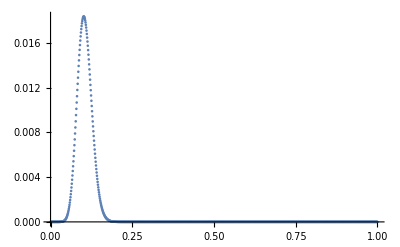

```mathematica
ListPlot[%,DataRange->{0,1}, PlotRange->All]
```

```mathematica
Export[]
```

```mathematica
%
```